```mathematica
ClearAll["Global`*"];
```

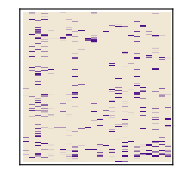

```mathematica
dat = Import["/Users/csfloyd/Dropbox/Projects/GlycanAnalysis/GlycanData.xlsx",{"Data",1}][[1;;-1;;4,1;;-1;;4]];
cBF[z_]:=Blend[ColorData["LakeColors"]/@{0,1},1-z];
cMin = 0;
cMax = 5;
MatrixPlot[dat,AspectRatio->1,ImageSize->Small,ColorFunction->(cBF[Rescale[#,{cMin,cMax}]]&),ColorFunctionScaling->False,Frame->True,FrameTicks->None]
```

```mathematica
mat = Import["/Users/csfloyd/Dropbox/Projects/GlycanAnalysis/GlycanData.xlsx",{"Data",1}]
Dimensions[mat]
```

{611,96}

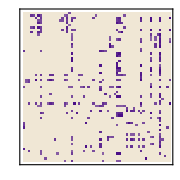

```mathematica
dat = Import["/Users/csfloyd/Dropbox/Projects/GlycanAnalysis/2000016_TableS3.xls",{"Data",1}][[2;;,2;;]]//Transpose;
cBF[z_]:=Blend[ColorData["LakeColors"]/@{0,1},z];
cMin = -5;
cMax = 0;
MatrixPlot[dat,AspectRatio->1,ImageSize->Small,ColorFunction->(cBF[Rescale[#,{cMin,cMax}]]&),ColorFunctionScaling->False,Frame->True,FrameTicks->None]
```

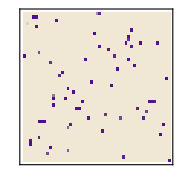

```mathematica
(*dat = ToExpression[Import["/Users/csfloyd/Dropbox/Projects/GlycanAnalysis/atlas_binding_matrix.xlsx",{"Data",1}][[2;;,2;;]]];*)

data=Import["/Users/csfloyd/Dropbox/Projects/GlycanAnalysis/atlas_binding_matrix.xlsx",{"Sheets","Kd_filled_uM"}];

(*First row is header (epitope sequences),first column is TCR names*)
epitopeLabels=data[[1,2;;]];
tcrLabels=data[[2;;,1]];
dat=-data[[2;;,2;;]]//N//Transpose;   (*numeric matrix,drop headers*)


cBF[z_]:=Blend[ColorData["LakeColors"]/@{0,1},1-z];
cMin = -300;
cMax = 0;
MatrixPlot[dat,AspectRatio->1,ImageSize->Small,ColorFunction->(cBF[Rescale[#,{cMin,cMax}]]&),ColorFunctionScaling->False,Frame->True,FrameTicks->None]
```

```mathematica
Needs["HierarchicalClustering`"]

matrixLog=dat;

(*Cluster rows and columns*)
rowCluster=Agglomerate[matrixLog->tcrLabels,Linkage->"Ward",DistanceFunction->SquaredEuclideanDistance];

colCluster=Agglomerate[Transpose[matrixLog]->epitopeLabels,Linkage->"Ward",DistanceFunction->SquaredEuclideanDistance];

(*Extract sorted labels directly from cluster leaf order*)
tcrOrdered=Flatten[rowCluster/. Cluster[d_,__]:>d];
epitopeOrdered=Flatten[colCluster/. Cluster[d_,__]:>d];

(*Get index order*)
rowOrder=Flatten[Position[tcrLabels,#]&/@tcrOrdered];
colOrder=Flatten[Position[epitopeLabels,#]&/@epitopeOrdered];

(*Reorder and plot*)
MatrixPlot[matrixLog[[rowOrder,colOrder]],ColorFunction->(Blend[{RGBColor[0.08,0.38,0.75],White},#]&),ColorFunctionScaling->True,FrameTicks->{{Table[{i,Style[tcrOrdered[[i]],8,FontFamily->"Courier"]},{i,1,Length[tcrOrdered]}],None},{Table[{j,Rotate[Style[epitopeOrdered[[j]],7,FontFamily->"Courier"],90 Degree]},{j,1,Length[epitopeOrdered]}],None}},Frame->True,FrameLabel->{Style["TCR",11],Style["Epitope",11]},PlotLegends->BarLegend[Automatic,LegendLabel->"log\[Subscript]10 Kd (μM)"],ImageSize->{800,500},PlotLabel->Style["Ward-clustered TCR × Epitope matrix",13,Bold]]
```

Agglomerate::list: List expected at position 1 in Agglomerate[«1»].

Agglomerate::nelist: Argument {} at position 1 is not a nonempty list.

Part::pkspec1: The expression Agglomerate[{},{},{}] cannot be used as a part specification.

MatrixPlot::mat0: Argument {{-300.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,«41»},{-300.,-300.,-300.,-0.321,-13.7,-300.,-300.,-300.,-300.,-300.,«41»},{-300.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,«41»},{-300.,-270.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,«41»},{-300.,-300.,-300.,-300.,-5.5,-300.,-300.,-300.,-300.,-300.,«41»},{«1»},{-300.,-300.,«7»,-300.,«41»},{-300.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,«41»},{-300.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,«41»},{-300.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,«41»},«36»}⟦«1»⟧ at position 1 is not a matrix.

```mathematica
(*Cluster rows—pass as list of row vectors*)rowCluster=Agglomerate[Table[matrixLog[[i]],{i,Length[tcrLabels]}]->tcrLabels,Linkage->"Ward",DistanceFunction->SquaredEuclideanDistance];

(*Cluster cols—pass as list of column vectors*)
colCluster=Agglomerate[Table[matrixLog[[All,j]],{j,Length[epitopeLabels]}]->epitopeLabels,Linkage->"Ward",DistanceFunction->SquaredEuclideanDistance];

(*Extract leaf order*)
tcrOrdered=Flatten[rowCluster/. Cluster[d_,__]:>d];
epitopeOrdered=Flatten[colCluster/. Cluster[d_,__]:>d];

rowOrder=Flatten[Position[tcrLabels,#]&/@tcrOrdered];
colOrder=Flatten[Position[epitopeLabels,#]&/@epitopeOrdered];

(*Plot*)
MatrixPlot[matrixLog[[rowOrder,colOrder]],ColorFunction->(Blend[{RGBColor[0.08,0.38,0.75],White},#]&),ColorFunctionScaling->True,FrameTicks->{{Table[{i,Style[tcrOrdered[[i]],8,FontFamily->"Courier"]},{i,1,Length[tcrOrdered]}],None},{Table[{j,Rotate[Style[epitopeOrdered[[j]],7,FontFamily->"Courier"],90 Degree]},{j,1,Length[epitopeOrdered]}],None}},Frame->True,FrameLabel->{Style["TCR",11],Style["Epitope",11]},PlotLegends->BarLegend[Automatic,LegendLabel->"log\[Subscript]10 Kd (μM)"],ImageSize->{800,500},PlotLabel->Style["Ward-clustered TCR × Epitope matrix",13,Bold]]
```

Part::partw: Part 47 of {{-300.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,«41»},{-300.,-300.,-300.,-0.321,-13.7,-300.,-300.,-300.,-300.,-300.,«41»},{-300.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,«41»},{-300.,-270.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,«41»},{-300.,-300.,-300.,-300.,-5.5,-300.,-300.,-300.,-300.,-300.,«41»},{«1»},{-300.,-300.,«7»,-300.,«41»},{-300.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,«41»},{-300.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,«41»},{-300.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,«41»},«36»} does not exist.

Part::partw: Part 48 of {{-300.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,«41»},{-300.,-300.,-300.,-0.321,-13.7,-300.,-300.,-300.,-300.,-300.,«41»},{-300.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,«41»},{-300.,-270.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,«41»},{-300.,-300.,-300.,-300.,-5.5,-300.,-300.,-300.,-300.,-300.,«41»},{«1»},{-300.,-300.,«7»,-300.,«41»},{-300.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,«41»},{-300.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,«41»},{-300.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,«41»},«36»} does not exist.

Part::partw: Part 49 of {{-300.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,«41»},{-300.,-300.,-300.,-0.321,-13.7,-300.,-300.,-300.,-300.,-300.,«41»},{-300.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,«41»},{-300.,-270.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,«41»},{-300.,-300.,-300.,-300.,-5.5,-300.,-300.,-300.,-300.,-300.,«41»},{«1»},{-300.,-300.,«7»,-300.,«41»},{-300.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,«41»},{-300.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,«41»},{-300.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,«41»},«36»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Agglomerate::xnum: A nonnumeric, negative or complex distance or dissimilarity value was computed; distances and dissimilarities must be nonnegative and real valued.

Agglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

Agglomerate::nelist: Argument {} at position 1 is not a nonempty list.

Part::pkspec1: The expression Agglomerate[{},{},{}] cannot be used as a part specification.

MatrixPlot::mat0: Argument {{-300.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,«41»},{-300.,-300.,-300.,-0.321,-13.7,-300.,-300.,-300.,-300.,-300.,«41»},{-300.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,«41»},{-300.,-270.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,«41»},{-300.,-300.,-300.,-300.,-5.5,-300.,-300.,-300.,-300.,-300.,«41»},{«1»},{-300.,-300.,«7»,-300.,«41»},{-300.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,«41»},{-300.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,«41»},{-300.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,-300.,«41»},«36»}⟦«1»⟧ at position 1 is not a matrix.